# PDE solving for a spherically symmetric case

## Considering the realist case in cosmology:

```mathematica
Clear["Global`*"];
```

Cosmological parameters:

```mathematica
w=-0.9;Ωm=0.3;
```

The equation for the Hubble derivative:

```mathematica
dlnHdlna = -(Ωm + (1+3w)(1-Ωm)Exp[-3w lna])/(2Ωm + 2(1-Ωm)Exp[-3w lna]);
```

The equation for the potential for the given Ωm and w0

```mathematica
ψSol = DSolve[(ψ''[lna] +(3+dlnHdlna)ψ'[lna]+(2-(3Ωm)/(2Ωm + 2(1-Ωm)Exp[-3w lna])+dlnHdlna)ψ[lna]== 0),ψ[lna], lna]
```

{{ψ[lna]→(0.456332 C[2] Hypergeometric2F1[-0.555556,0.12963,0.0740741,-2.33333 ⅇ^(2.7 lna)])/((ⅇ^(2.7 lna))^0.925926)+(1. C[1] Hypergeometric2F1[0.37037,1.05556,1.92593,-2.33333 ⅇ^(2.7 lna)])/((ⅇ^(2.7 lna))^(3.83781×10^-17))}}

Only one solution is the relevant one (it becomes constant as lna -> -∞):

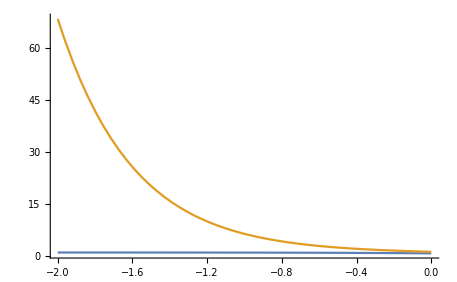

```mathematica
Plot[{ψ[lna]/.ψSol/.C[2]->0/.C[1]->1,ψ[lna]/.ψSol/.C[1]->0/.C[2]->1//Simplify},{lna,-2,0},PlotRange->All]
```

We now need to choose the radial profile of ψ. As is well known, every spherically symmetric function can be expanded in terms of j_even(k r),  here we consider a profile with only j_0 contribution and neglect higher orders . Let us consider a single spherical wave mode with wave number k. Note that in the following k and r will use units of H_0 so that everything is dimensionless.

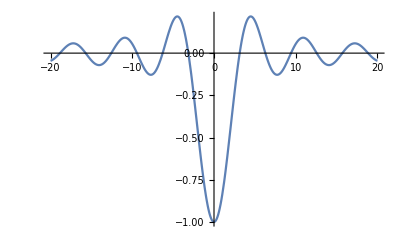

```mathematica
Plot[-SphericalBesselJ[0,x],{x,-20,20},PlotRange->All]
```

```mathematica
ψ[lna_,r_]:= amplitude Hypergeometric2F1[2/5,11/10,2,-7/3 ⅇ^(5 lna/2)] SphericalBesselJ[0,k r];
```

Let’s call π̃ of eq. (4.59) “p[lna,r]”.

Solutions for different initial curvature (different densities);

```mathematica
numAmplitude=12;
For[i=0,i<numAmplitude+1,++i;amplitude[i]= -4*2^i/100;nsol[i] =NDSolve[{(Derivative[2,0][p][lna,r] + (1-3w-dlnHdlna)Derivative[1,0][p][lna,r]+(3w(dlnHdlna-1)-D[dlnHdlna,lna])p[lna,r]+3w ψ[lna,r]-D[ψ[lna,r],lna] ==(2-3w)/(2(Ωm Exp[-lna]+(1-Ωm)Exp[-(1+3w)lna]))(Derivative[0,1][p][lna,r])^2),p[-8,r] == 0,Derivative[1,0][p][-8,r]== ψ[-8,r]/2}/.amplitude-> amplitude[i]/.k-> 20,p,{lna, -7.5,0},{r,-2,2},MaxStepSize-> 0.02];]
```

Now we find the blowup redshift for each amplitude!

```mathematica
step=0.01;
lnaini =-7.5;
```

```mathematica
For[i=0,i<numAmplitude+1,i++;
For[lna=lnaini,lna<0,lna += step;If[Abs[p[lna,0] /√(Ωm Exp[-lna]+(1-Ωm)Exp[-(1+3w)lna])/.Ωm-> 3/10/.w-> -0.9/.nsol[i]][[1]]>10^4,dataBlowup[i]=lna;Print["i:",i," amplitude:",amplitude[i], "  Blowup a:",dataBlowup[i]];Break[],Continue[]];]];
```

i:1 amplitude:-2/25  Blowup a:-1.24

i:2 amplitude:-4/25  Blowup a:-1.95

i:3 amplitude:-8/25  Blowup a:-2.66

i:4 amplitude:-16/25  Blowup a:-3.37

i:5 amplitude:-32/25  Blowup a:-4.07

i:6 amplitude:-64/25  Blowup a:-4.71

i:7 amplitude:-128/25  Blowup a:-5.28

i:8 amplitude:-256/25  Blowup a:-5.78

i:9 amplitude:-512/25  Blowup a:-6.19

i:10 amplitude:-1024/25  Blowup a:-6.53

i:11 amplitude:-2048/25  Blowup a:-6.81

i:12 amplitude:-4096/25  Blowup a:-7.04

i:13 amplitude:-8192/25  Blowup a:-7.23

```mathematica
data = Table[{-amplitude[i],Exp[-dataBlowup[i]]-1},{i,1,numAmplitude+1}];
```

```mathematica
logline = Fit[Log[data], {1,x,x^2},x];
```

```mathematica
A1=ListLogLogPlot[data, PlotRange->All, ImageSize->Large, AxesLabel->{Style["ρ_ini",FontSize->24],Style["1+z_b",FontSize->24]}, PlotStyle->Red];
```

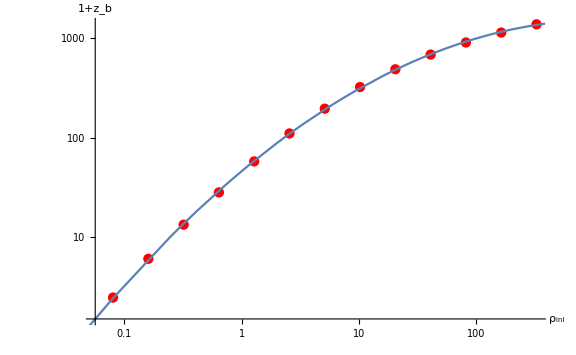

```mathematica
Show[A1 ,Plot[logline,{x,-10,200},PlotLegends->logline]]
```

## Considering only non-linear term in the equation:

```mathematica
Clear["Global`*"];
```

Cosmological parameters:

```mathematica
w=-0.9;Ωm=0.3;
```

We consider again similar potential but without time dependence!

```mathematica
ψ[lna_,r_]:= amplitude SphericalBesselJ[0,k r];
```

Let’s call π̃ of eq. (4.59) “p[lna,r]”.

Solutions for different initial curvature (different densities);

```mathematica
numAmplitude=12;
For[i=0,i<numAmplitude+1,++i;amplitude[i]= -6*2^i/100;nsol[i] =NDSolve[{(Derivative[2,0][p][lna,r]  ==(2-3w)/(2(Ωm Exp[-lna]+(1-Ωm)Exp[-(1+3w)lna]))(Derivative[0,1][p][lna,r])^2),p[-8,r] == 0,Derivative[1,0][p][-8,r]== ψ[-8,r]/2}/.amplitude-> amplitude[i]/.k-> 20,p,{lna, -7.5,0},{r,-2,2},MaxStepSize-> 0.02];]
```

Now we find the blowup redshift for each amplitude!

```mathematica
step=0.01;
lnaini =-7.5;
For[i=0,i<numAmplitude+1,i++;
For[lna=lnaini,lna<0,lna += step;If[Abs[p[lna,0] /√(Ωm Exp[-lna]+(1-Ωm)Exp[-(1+3w)lna])/.nsol[i]][[1]]>10^4,dataBlowup[i]=lna;Print["i:",i," amplitude:",amplitude[i], "  Blowup a:",dataBlowup[i]];Break[],Continue[]];]];
```

i:1 amplitude:-3/25  Blowup a:-3.62

i:2 amplitude:-6/25  Blowup a:-4.09

i:3 amplitude:-12/25  Blowup a:-4.55

i:4 amplitude:-24/25  Blowup a:-4.97

i:5 amplitude:-48/25  Blowup a:-5.36

i:6 amplitude:-96/25  Blowup a:-5.73

i:7 amplitude:-192/25  Blowup a:-6.06

i:8 amplitude:-384/25  Blowup a:-6.35

i:9 amplitude:-768/25  Blowup a:-6.61

i:10 amplitude:-1536/25  Blowup a:-6.84

i:11 amplitude:-3072/25  Blowup a:-7.04

i:12 amplitude:-6144/25  Blowup a:-7.21

i:13 amplitude:-12288/25  Blowup a:-7.35

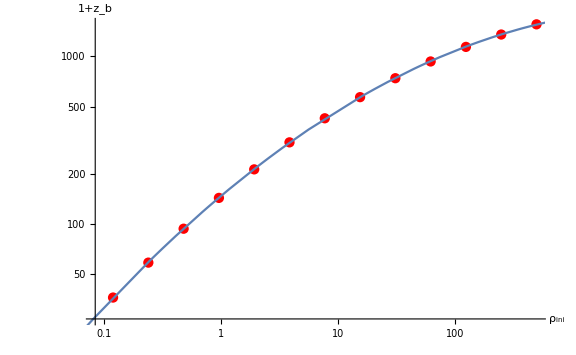

```mathematica
data = Table[{-amplitude[i],Exp[-dataBlowup[i]]-1},{i,1,numAmplitude+1}];
logline = Fit[Log[data], {1,x,x^2},x];

A1=ListLogLogPlot[data, PlotRange->All, ImageSize->Large, AxesLabel->{Style["ρ_ini",FontSize->24],Style["1+z_b",FontSize->24]}, PlotStyle->Red];

Show[A1 ,Plot[logline,{x,-10,200},PlotLegends->logline]]
```

## Considering only non-linear term and matter domination:

```mathematica
Clear["Global`*"];
```

Cosmological parameters:

```mathematica
w=-1;Ωm=1;
```

We consider again similar potential but without time dependence!

```mathematica
ψ[lna_,r_]:= amplitude SphericalBesselJ[0,k r];
```

Let’s call π̃ of eq. (4.59) “p[lna,r]”.

Solutions for different initial curvature (different densities);

```mathematica
numAmplitude=12;
For[i=0,i<numAmplitude+1,++i;amplitude[i]= -6*2^i/100;nsol[i] =NDSolve[{(Derivative[2,0][p][lna,r]  ==(2-3w)/(2(Ωm Exp[-lna]+(1-Ωm)Exp[-(1+3w)lna]))(Derivative[0,1][p][lna,r])^2),p[-8,r] == 0,Derivative[1,0][p][-8,r]== ψ[-8,r]/2}/.amplitude-> amplitude[i]/.k-> 20,p,{lna, -7.5,0},{r,-2,2},MaxStepSize-> 0.02];]
```

Now we find the blowup redshift for each amplitude!

```mathematica
step=0.01;
lnaini =-7.5;
For[i=0,i<numAmplitude+1,i++;
For[lna=lnaini,lna<0,lna += step;If[Abs[p[lna,0] /√(Ωm Exp[-lna]+(1-Ωm)Exp[-(1+3w)lna])/.nsol[i]][[1]]>10^4,dataBlowup[i]=lna;Print["i:",i," amplitude:",amplitude[i], "  Blowup a:",dataBlowup[i]];Break[],Continue[]];]];
```

i:1 amplitude:-3/25  Blowup a:-2.79

i:2 amplitude:-6/25  Blowup a:-3.3

i:3 amplitude:-12/25  Blowup a:-3.79

i:4 amplitude:-24/25  Blowup a:-4.26

i:5 amplitude:-48/25  Blowup a:-4.7

i:6 amplitude:-96/25  Blowup a:-5.11

i:7 amplitude:-192/25  Blowup a:-5.49

i:8 amplitude:-384/25  Blowup a:-5.85

i:9 amplitude:-768/25  Blowup a:-6.16

i:10 amplitude:-1536/25  Blowup a:-6.45

i:11 amplitude:-3072/25  Blowup a:-6.7

i:12 amplitude:-6144/25  Blowup a:-6.92

i:13 amplitude:-12288/25  Blowup a:-7.1

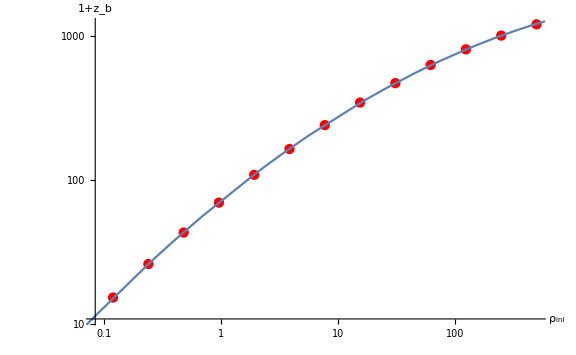

```mathematica
data = Table[{-amplitude[i],Exp[-dataBlowup[i]]-1},{i,1,numAmplitude+1}];
logline = Fit[Log[data], {1,x,x^2},x];

A1=ListLogLogPlot[data, PlotRange->All, ImageSize->Large, AxesLabel->{Style["ρ_ini",FontSize->24],Style["1+z_b",FontSize->24]}, PlotStyle->Red];

Show[A1 ,Plot[logline,{x,-10,200},PlotLegends->logline]]
```